```mathematica
Clear[a,b,fs,L];
(*using a generic L until I can figure out how to introduce it as a variable*)
(*trying to figure out how to define functions as peicewise in mathematica*)
(*f[x_]:=x*(1+Abs[x])/;-1≤x<1;
f[x_]:=f[x+2]/;x≥1OR x<-1; 
f[1],f[3]  *)
```

```mathematica
L=1;
fbas[x_]:=(1-x)(1+x^2)/;-L≤x<L
f[x_]:=fbas[Mod[x,2×L,-L]]
```

```mathematica
N[f[3]]
```

4.

```mathematica
(*Defining the function as peicewise*)
```

```mathematica
(*g[x_]:=Piecewise[{{x*(1+Abs[x]),-1<=0<1},{f[x+2],x≥1}}];
g[3] *)
```

12

```mathematica
(*Defining the shifted function via Prof. Clark*)
```

```mathematica
(*defining the function to be approximated by the Fourier series*)
a[0]=N[Integrate[f[x],{x,-L,L}]]
```

2.66667

```mathematica
a[n_]=(∫_-L^L x*(1+Abs[x])*Cos[(n*Pi*x)/L]ⅆx)/(2L)
```

0

```mathematica
b[n_]=FullSimplify[(∫_-L^L x*(1+Abs[x])*Sin[(n*Pi*x)/L]ⅆx)/L]
```

(-4+(4-4 n^2 π^2) Cos[n π]+6 n π Sin[n π])/(n^3 π^3)

```mathematica
coeffs=Table[{a[i],b[i]},{i,1,10}];
TableForm[coeffs]
```

0 | (-8+4 π^2)/π^3
0 | -2/π
0 | (-8+36 π^2)/(27 π^3)
0 | -1/π
0 | (-8+100 π^2)/(125 π^3)
0 | -2/(3 π)
0 | (-8+196 π^2)/(343 π^3)
0 | -1/(2 π)
0 | (-8+324 π^2)/(729 π^3)
0 | -2/(5 π)

```mathematica
coeffs[[1]]
```

{0,(-8+4 π^2)/π^3}

```mathematica
coeffs[[2,1]]
```

0

```mathematica
fs[k_,x_]:=coeffs[[k,1]]*Cos[k*Pi*x/L]+coeffs[[k,2]]*Sin[k*Pi*x/L]
```

```mathematica
fourier[n_,x_]:=a[0]+∑_(k=1)^n fs[k,x]
```

```mathematica
fourier[5,x]
```

2.66667+((-8+4 π^2) Sin[π x])/π^3-(2 Sin[2 π x])/π+((-8+36 π^2) Sin[3 π x])/(27 π^3)-Sin[4 π x]/π+((-8+100 π^2) Sin[5 π x])/(125 π^3)

```mathematica
fourier[10,x]
```

2.66667+((-8+4 π^2) Sin[π x])/π^3-(2 Sin[2 π x])/π+((-8+36 π^2) Sin[3 π x])/(27 π^3)-Sin[4 π x]/π+((-8+100 π^2) Sin[5 π x])/(125 π^3)-(2 Sin[6 π x])/(3 π)+((-8+196 π^2) Sin[7 π x])/(343 π^3)-Sin[8 π x]/(2 π)+((-8+324 π^2) Sin[9 π x])/(729 π^3)-(2 Sin[10 π x])/(5 π)

```mathematica
Off[General::stop];
fourier[10,x]
```

2.66667+((-8+4 π^2) Sin[π x])/π^3-(2 Sin[2 π x])/π+((-8+36 π^2) Sin[3 π x])/(27 π^3)-Sin[4 π x]/π+((-8+100 π^2) Sin[5 π x])/(125 π^3)-(2 Sin[6 π x])/(3 π)+((-8+196 π^2) Sin[7 π x])/(343 π^3)-Sin[8 π x]/(2 π)+((-8+324 π^2) Sin[9 π x])/(729 π^3)-(2 Sin[10 π x])/(5 π)

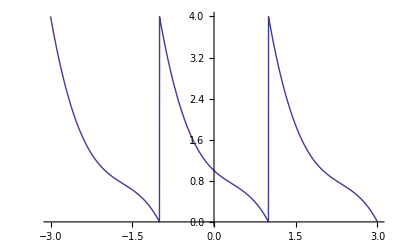

```mathematica
graphone=Plot[f[x],{x,-3,3}]
```

```mathematica
(*Manipulate[  consider manipulating k to find a reasonable value*)
```

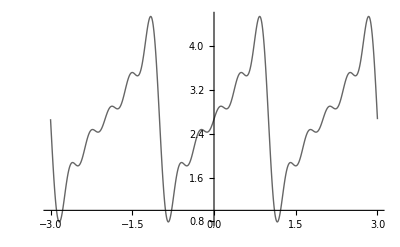

```mathematica
graphtwo=Plot[fourier[5,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

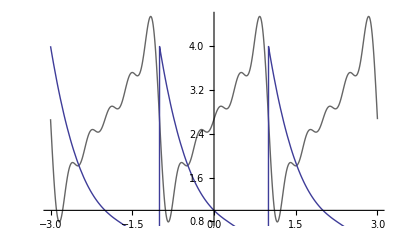

```mathematica
bothtwo=Show[graphtwo,graphone]
```

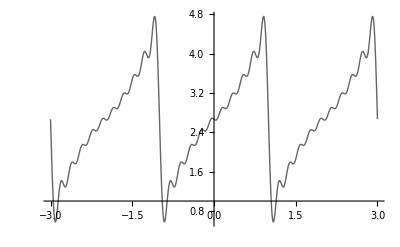

```mathematica
graphthree=Plot[fourier[10,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

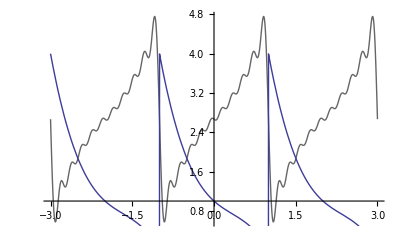

```mathematica
boththree=Show[graphthree,graphone]
```

```mathematica
graphsix=Plot[fourier[20,x],{x,-3,3},PlotStyle->GrayLevel[0.4]]
```

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 16 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 17 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 18 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 19 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 20 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 11 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 12 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 13 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 14 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 15 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 16 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 17 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 18 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 19 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 20 of {{0.`, 1.015227269269567`}, {0.`, -0.6366197723675814`}, {0.`, 0.4148571713759581`}, {0.`, -0.3183098861837907`}, {0.`, 0.2525838107433078`}, {0.`, -« 19 »}, {0.`, 0.18113914115614396`}, {0.`, -0.15915494309189535`}, {0.`, 0.14111713422233552`}, {0.`, -0.12732395447351627`}} does not exist.

Part::partw: Part 11 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 12 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 13 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 14 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

Part::partw: Part 15 of {{0, -8 + 4 π^2/π^3}, {0, -2/π}, {0, -8 + 36 π^2/27 π^3}, {0, -1/π}, {0, -8 + 100 π^2/125 π^3}, {0, -2/3 π}, {0, -8 + 196 π^2/343 π^3}, {0, -1/2 π}, {0, -8 + 324 π^2/729 π^3}, {0, -2/5 π}} does not exist.

$Aborted

```mathematica
bothsix=Show[graphsix,graphone]
```

Show::gcomb: Could not combine the graphics objects in Show[graphsix, GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], LineBox[List[List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], List[Skeleton[2]], Skeleton[409]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[-3, 3], List[0.`, 3.999999265306184`]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Scaled[0.02`], Scaled[0.02`]]]]]].

Show[graphsix,-Graphics-]

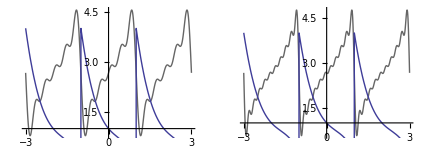

```mathematica
Show[GraphicsRow[{bothtwo,boththree,bothsix}]]
```

```mathematica
(*Begin of Problem #4*)
```